## Calculating ω and v0 in Rotating Reference Frame (To Compare to ω and v0 Calculated in Non-Rotating)

```mathematica
ClearAll["Global`*"]
```

```mathematica
dataold=Import[FileNames["NIRF_puck_x_y.csv",NotebookDirectory[],2][[1]]]
```

{{0,30.217,-7.98},{0.033,27.387,-9.953},{0.067,23.681,-11.683},{0.1,17.381,-13.721},{0.133,13.786,-14.267},{0.167,11.272,-14.26},{0.2,7.834,-14.013},{0.233,4.384,-13.403},{0.267,1.223,-12.424},{0.3,-1.775,-11.013},{0.333,-4.595,-9.281},{0.367,-7.054,-7.311},{0.4,-9.136,-5.289},{0.433,-10.928,-3.026},{0.467,-12.383,-0.552},{0.5,-13.462,2.025},{0.533,-14.227,4.704},{0.566,-14.796,7.44},{0.6,-15.04,10.157},{0.633,-14.925,12.865},{0.666,-14.528,15.589},{0.7,-13.818,18.278},{0.733,-12.869,20.794},{0.766,-11.77,23.069},{0.8,-10.61,25.248},{0.833,-9.098,27.245},{0.866,-7.457,29.057},{0.901,-5.783,30.702},{0.933,-4.085,32.284},{0.966,-2.23,33.731},{1,-0.29,35.097},{1.033,1.865,36.283},{1.066,4.251,37.259},{1.1,6.751,38.038},{1.133,9.47,38.584},{1.166,12.024,38.975},{1.2,14.934,39.057},{1.233,17.698,39.029},{1.266,20.369,38.757},{1.3,23.017,38.344},{1.333,25.343,37.864},{1.366,27.733,37.253},{1.399,30.192,36.477},{1.433,32.48,35.678},{1.466,35.057,34.622},{1.499,37.396,33.53},{1.533,39.84,32.3}}

```mathematica
data=Transpose[dataold];
```

Time Information in ti:

```mathematica
ti=data[[1,All]];
```

```mathematica
tfinal=ti[[-1]]+(ti[[-1]]*.03)
```

1.57899

{x,y} coordinate information in ci:

```mathematica
ci=data[[2;;,All]];
```

```mathematica
sol=ParametricNDSolve[{xtheory''[t]==ω*(ω*xtheory[t])+2*ω*ytheory'[t],ytheory''[t]==ω*(ω*ytheory[t])-2*ω*xtheory'[t],xtheory[0]==x0,ytheory[0]==y0,xtheory'[0]==v0*Cos[θ],ytheory'[0]==v0*Sin[θ]},{xtheory,ytheory},{t,0,tfinal},{ω,x0,y0,v0,θ}];
```

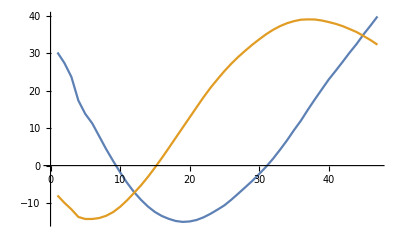

```mathematica
ListLinePlot[ci]
```

```mathematica
transformedData={ConstantArray[Range@Length[ci],Length[ti]]//Transpose,ConstantArray[ti,Length[ci]],ci}~Flatten~{{2,3},{1}};
```

Now the data is in following format: {dependent variable number (so like x=1 or y=2 or z=3), time (from ti), value}

This above assumed that originally it was like {t,x,y}

```mathematica
NIRFraw=Import[FileNames["NIRF_puck_x_y.csv",NotebookDirectory[],2][[1]]];
```

```mathematica
xandy={#[[2]],#[[3]]}&/@NIRFraw;
```

```mathematica
xandy[[1,1]]
```

30.217

```mathematica
x0guess=xandy[[1,1]]
```

30.217

```mathematica
y0guess=xandy[[1,2]]
```

-7.98

Next step is to use the guesses we got from analyzing motion in the non-rotating reference frame:

```mathematica
sol=ParametricNDSolveValue[{xtheory''[t]==ω*(ω*xtheory[t])+2*ω*ytheory'[t],ytheory''[t]==ω*(ω*ytheory[t])-2*ω*xtheory'[t],xtheory[0]==x0,ytheory[0]==y0,xtheory'[0]==v0*Cos[θ],ytheory'[0]==v0*Sin[θ]},{xtheory,ytheory},{t,0,tfinal},{ω,x0,y0,v0,θ}];
```

```mathematica
model[ω_,x0_,y0_,v0_,θ_][i_,t_]:=Through[sol[ω,x0,y0,v0,θ][t],List][[i]]/;And@@NumericQ/@{ω,x0,y0,v0,θ,i,t}
```

```mathematica
fit=NonlinearModelFit[transformedData,model[ω,x0,y0,v0,θ][i,t],{ω,x0,y0,v0,θ},{i,t}];
```

```mathematica
fit=NonlinearModelFit[transformedData,{model[ω,x0,y0,v0,θ][i,t],ω>0,x0guess-0.5<x0<x0guess+.5,y0guess-0.5<y0<y0guess+.5},{{ω,1.5},{x0,30},{y0,-8},{v0,122},{θ,-140Degree}},{i,t}];
```

```mathematica
fit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
ω | 1.7258 | 0.0702392 | 24.5703 | 1.98951×10^-41
x0 | 29.717 | 1.53958 | 19.3021 | 1.4478×10^-33
y0 | -8.48 | 2.2489 | -3.77073 | 0.000292506
v0 | 90.4996 | 3.47303 | 26.0578 | 2.00065×10^-43
θ | -2.55918 | 0.0849629 | -30.1211 | 1.84399×10^-48

```mathematica
e=fit["ParameterTableEntries"]
```

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{1.7258,0.0702392,24.5703,1.98951×10^-41},{29.717,1.53958,19.3021,1.4478×10^-33},{-8.48,2.2489,-3.77073,0.000292506},{90.4996,3.47303,26.0578,2.00065×10^-43},{-2.55918,0.0849629,-30.1211,1.84399×10^-48}}

```mathematica
w1=e[[1,1]]
```

1.7258

```mathematica
w2=e[[1,1]]+e[[1,1]].2
```

2.07096

```mathematica
w3=e[[1,1]]-e[[1,1]].2
```

1.38064

```mathematica
x0=e[[2,1]]
```

29.717

```mathematica
y0=e[[3,1]]
```

-8.48

```mathematica
v0=e[[4,1]]
```

90.4996

```mathematica
θ=e[[5,1]]
```

-2.55918

```mathematica
s1=NDSolve[{xtheory''[t]==ω*(ω*xtheory[t])+2*ω*ytheory'[t],ytheory''[t]==ω*(ω*ytheory[t])-2*ω*xtheory'[t],xtheory[0]==x0,ytheory[0]==y0,xtheory'[0]==v0*Cos[θ],ytheory'[0]==v0*Sin[θ]}/.{ω->w1},{xtheory[t],ytheory[t]},{t,0,tfinal}]
```

{{xtheory[t]→InterpolatingFunction[…][t],ytheory[t]→InterpolatingFunction[…][t]}}

```mathematica
X1theory[t_]=xtheory[t]/.Flatten[s1];
Y1theory[t_]=ytheory[t]/.Flatten[s1];
```

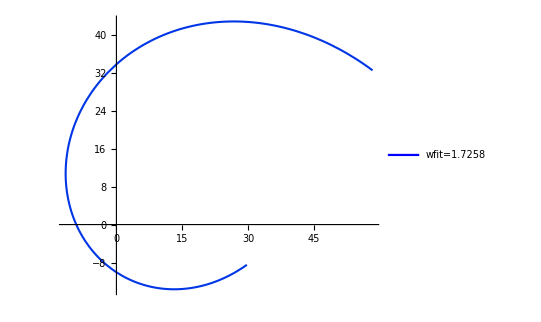

```mathematica
pw1=ParametricPlot[{X1theory[t],Y1theory[t]},{t,0,tfinal},PlotStyle->Directive[RGBColor[0.,0.21,0.9],AbsoluteThickness[1.5]],PlotLegends->LineLegend[{Blue},{"wfit="<>ToString[w1]}]]
```

```mathematica
s2=NDSolve[{xtheory''[t]==ω*(ω*xtheory[t])+2*ω*ytheory'[t],ytheory''[t]==ω*(ω*ytheory[t])-2*ω*xtheory'[t],xtheory[0]==x0,ytheory[0]==y0,xtheory'[0]==v0*Cos[θ],ytheory'[0]==v0*Sin[θ]}/.{ω->w2},{xtheory[t],ytheory[t]},{t,0,tfinal}]
```

{{xtheory[t]→InterpolatingFunction[…][t],ytheory[t]→InterpolatingFunction[…][t]}}

```mathematica
X2theory[t_]=xtheory[t]/.Flatten[s2];
Y2theory[t_]=ytheory[t]/.Flatten[s2];
```

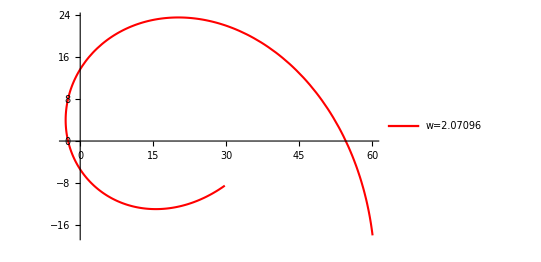

```mathematica
pw2=ParametricPlot[{X2theory[t],Y2theory[t]},{t,0,tfinal},PlotStyle->Directive[Red,AbsoluteThickness[1.5]],PlotLegends->LineLegend[{Red},{"w="<>ToString[w2]}]]
```

```mathematica
s3=NDSolve[{xtheory''[t]==ω*(ω*xtheory[t])+2*ω*ytheory'[t],ytheory''[t]==ω*(ω*ytheory[t])-2*ω*xtheory'[t],xtheory[0]==x0,ytheory[0]==y0,xtheory'[0]==v0*Cos[θ],ytheory'[0]==v0*Sin[θ]}/.{ω->w3},{xtheory[t],ytheory[t]},{t,0,tfinal}]
```

{{xtheory[t]→InterpolatingFunction[…][t],ytheory[t]→InterpolatingFunction[…][t]}}

```mathematica
X3theory[t_]=xtheory[t]/.Flatten[s3];
Y3theory[t_]=ytheory[t]/.Flatten[s3];
```

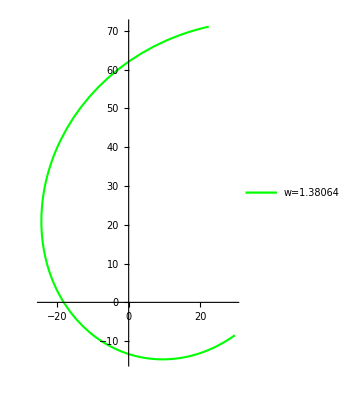

```mathematica
pw3=ParametricPlot[{X3theory[t],Y3theory[t]},{t,0,tfinal},PlotStyle->Directive[Green,AbsoluteThickness[1.5]],PlotLegends->LineLegend[{Green},{"w="<>ToString[w3]}]]
```

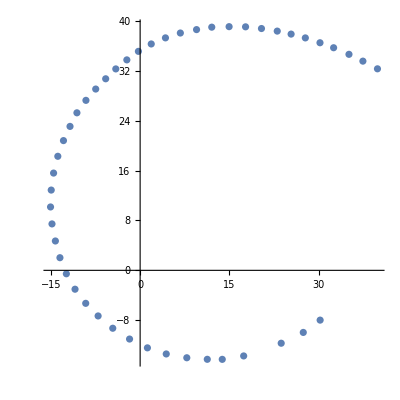

```mathematica
p1=ListPlot[xandy, AspectRatio->1]
```

I’m not actually sure about the radius of this thing. it is r=116/2 cm

```mathematica
cir=Graphics[Circle[{0,0},116/2]];
```

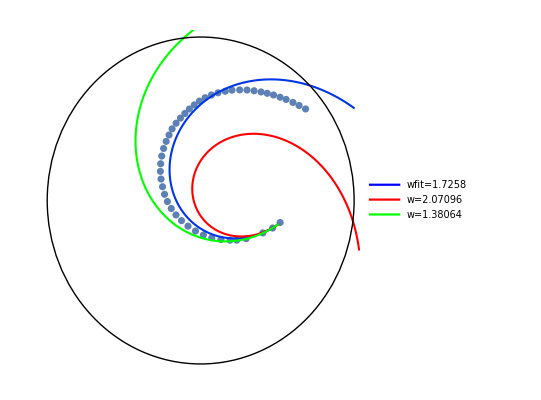

```mathematica
Show[p1,pw1,pw2,pw3,cir,PlotRange->{{-116/2,116/2},{-116/2,116/2}},Frame->False,FrameTicks->None,Ticks->None,Axes->False]
```